# Linear Algebra

## Solving Linear Systems

In this notebook, we’ll look at Mathematica operations involving concepts from linear algebra. Linear algebra, perhaps more than any other area of math, benefits from computer algebra systems. If you think back to what it was like learning to multiply matrices or put them into reduced form, you should remember long, tedious, and error-prone computations. Many of the algorithms learned in linear algebra courses have built-in implementations in Mathematica. This notebook will explore some of those functions and investigate some others.

A fundamental problem in linear algebra is solving a linear system. Suppose that we want to solve the system

-2 x_1 - 3 x_2+ 3 x_3=-1
	   -  2 x_2+2 x_3=-2
  5 x_1  + 2 x_2 -   x_3= 6

There are many ways to solve this, and we examine three of them here.

## Solution 1

A strategy introduced early in a course in linear algebra is to form an augmented matrix from the system and then row reduce to the identity, from which we can infer the solution. This is easy to do in  Mathematica. First, you do not need to use the Mathematica palette - a matrix is just a list of lists, with each sublist representing one row. Hence, we can define the matrix aug as follows.

```mathematica
aug = {{-2, -3, 3, -1}, {0, -2, 2, -2}, {5, 2, -1, 6}}
```

{{-2,-3,3,-1},{0,-2,2,-2},{5,2,-1,6}}

```mathematica
RowReduce[aug]
```

{{1,0,0,-1},{0,1,0,10},{0,0,1,9}}

If we want to see this interpreted as  matrix (which makes the result significantly easier to read), we can use the function MatrixForm.

```mathematica
{{1,0,0,-1},{0,1,0,10},{0,0,1,9}}//MatrixForm
```

(1 | 0 | 0 | -1
0 | 1 | 0 | 10
0 | 0 | 1 | 9)

We conclude that x_1=-1, x_2 = 10, x_3= 9.

### Solution 2

Another way to solve this problem would be to interpret the system as a matrix equation A x = b, where A is the matrix of coefficients, x is the vector of unknowns, and b is the vector of entries on the right side of the equals sign. If the matrix A happens to be invertible, then the solution to the system will be x = A^-1 b. This is also easy to do in Mathematica. Mathematica handles column vectors as matrices having a single column and row vectors as matrices with a single row. When manually entering a column vector, you would need to use many curly braces. On the other hand, entering a row vector is easy. We can avoid entering column vectors by using the Transpose function.

```mathematica
A = {{-2, -3, 3}, {0, -2, 2}, {5, 2, -1}}
```

{{-2,-3,3},{0,-2,2},{5,2,-1}}

```mathematica
b = Transpose[{{-1, -2, 6}}]
```

{{-1},{-2},{6}}

We should check to make sure that A is invertible. Two methods we have learned in the past include checking to see that the determinant of A is not 0 and that A row reduces to the identity matrix (both  of which are parts of the Invertible Matrix Theorem).

```mathematica
RowReduce[A]==IdentityMatrix[3]
```

True

```mathematica
Det[A] ≠0
```

True

When we are multiplying matrix type objects together, we want to ensure that we are using the special multiplication from linear algebra. In Mathematica, matrix multiplication is done with the function Dot, which has shorthand “.”. The inverse of a matrix can be found with the command Inverse.

```mathematica
A.Inverse[A]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Inverse[A].A
```

{{1,0,0},{0,1,0},{0,0,1}}

So to compute A^-1 b, we just type

```mathematica
Inverse[A].b
```

{{-1},{10},{9}}

### Solution 3

A third way to solve linear systems is to use the built in function LinearSolve.

```mathematica
LinearSolve[A,b]
```

{{-1},{10},{9}}

### Matrix formulas

Mathematica has convenient features for constructing the sorts of matrices that show up in research and application. First, we can create matrices where the (i, j) entry is given by a formula. The function Array takes two arguments. The first argument is a function of two variables that specifies the formula for the entries. The second argument is for the dimensions of the matrix.

```mathematica
Array[f[#1, #2]&, {2, 2}]
```

{{f[1,1],f[1,2]},{f[2,1],f[2,2]}}

```mathematica
%//MatrixForm
```

(f[1,1] | f[1,2]
f[2,1] | f[2,2])

Another type of matrix that regularly occurs in practice is a block matrix, which can be created using a function called ArrayFlatten. Suppose that A, B, C, D are matrices so that the number of columns in A (and B)  is respectively equal to the number of columns in C (and D), and that the number of rows in A (and C) is respectively equal the number of rows in B (and D). To make the rectangular block matrix

(A | B
C | D)

one would use the command ArrayFlatten[{{A, B}, {C, D}}. Here is an example.

```mathematica
A = RandomInteger[9, {2,2}];
ArrayFlatten[{{A, A}, {A, A}}]
```

{{2,9,2,9},{6,2,6,2},{2,9,2,9},{6,2,6,2}}

```mathematica
%//MatrixForm
```

(2 | 9 | 2 | 9
6 | 2 | 6 | 2
2 | 9 | 2 | 9
6 | 2 | 6 | 2)

Compare with

```mathematica
{{A, A}, {A, A}}//MatrixForm
```

((2 | 9
6 | 2) | (2 | 9
6 | 2)
(2 | 9
6 | 2) | (2 | 9
6 | 2))

### Exercises

#### Exercise 1

Solve the linear system

x - 4 y + 3 z =    5
-x - 2 y + 3z = -1 
  x - 3 y +     z  =  0

using each of the three methods outlined in the lesson.

#### Exercise 2

Consider the matrix

A = (-5 | -4 | -1 | -5
-5 | 0 | -4 | 1
5 | 2 | 2 | 2
3 | 1 | 3 | 1)

Is A invertible? If so, find A^-1 and verify that A A^-1= I.

#### Exercise 3

Let

A_θ= (cos θ | -sin θ
sin θ | cos θ).

Then, the linear transformation on ℝ^2 defined by x → A_θ x rotates a vector in the plane counter-clockwise through an angle θ, and so it must be that A_α A_β = A_(α+β).

1. Use the fact stated above and matrix multiplication to verify that cos(α + β) = cos α cos β - sin α sin β and sin (α + β) = sin α cos β + cos α sin β.

2. Find an identity for sin 3θ  in terms of sin θ and cos θ.

#### Exercise 4

Let A_n denote the n × n matrix

(1^2 | 2^2 | … | n^2
(n+1)^2 | (n+2)^2 | … | (2n)^2
⋮ | ⋮ | ⋱ | ⋮
((n-1)n+1)^2 | ((n-1)n+2)^2 | … | (n^2)^2)

1. Using Array, write a function A[n_] that creates A_n for a given n.

2. Display A_8 using MatrixForm.

3. Generate data and make a conjecture as to which values of n make A_n invertible.

#### Exercise 5

You might remember learning a technique called Cramer’s rule,which can be used to compute x_i, the ith component of the solution to a linear system A x = b when A is invertible (see https://en.wikipedia.org/wiki/Cramer%27 s_rule). Cramer’s rule asserts that x_i is equal to a ratio of determinants. The denominator is the determinant of A, and the numerator is the determinant of the matrix resulting from replacing the ith column of A with the vector b.

1. Write a function called CramersRule[A_, b_, i_] which returns x_i, the ith component of the solution to the system A x = b. (Hint: it’s easier to replace a row of a matrix than a column. Additionally, the command ReplacePart may come in handy.)

2. Use CramersRule to compute x_4 in the system

(0 | 1 | 8 | 4
8 | 5 | 10 | 10
4 | 4 | 10 | 9
7 | 3 | 4 | 5)x = (1
1
1
1).

3. Find the solution to the linear system in Exercise 1 using CramersRule.

#### Exercise 6

Define the matrix-valued function

A(s, t) = (1 | s
t | 1),

and let p_0= (0
0), p_1= (1
0), p_2=(1
1), p_3=(0
1).

1. Considering each p_i as the position vector of a point in ℝ^2, use Graphics and Polygon to render the parallelogram P determined by these points.

2. Use Area to find the area of P.

3. Using Manipulate for the parameters -5 ≤ s, t, ≤ 5, render the parallelogram determined by the points having position vectors A(s, t) p_i for 0 ≤ i ≤ 3. (In fact, this is the the image of the parallelogram P under the linear transformation x → A(s, t) x.) Fix the plot range so that -10 ≤ x, y ≤ 10 using PlotRange -> 10. Play around with the parameters s, t and describe how they affect the shape of the parallelogram.

4. Compute both the area of the parallelogram with position vectors A(s,t) p_i and det A(s,t) for some values of s, t of your choosing. Comment on the relationship that you notice.

## Eigenvalues, eigenvectors, and diagonalization

One of the most important ideas in linear algebra is the diagonalization of matrices. (See https://en.wikipedia.org/wiki/Diagonalizable_matrix for a refresher.) A matrix is diagonalizable if there is a basis of eigenvectors. I sincerely hope you haven’t forgotten what an eigenvector is, but if so, make sure to see https://en.wikipedia.org/wiki/Eigenvalues_and_eigenvectors.  Thankfully computing eigenvectors and eigenvalues in Mathematica is quite easy.  Not surprisingly, the functions Eigenvalues and Eigenvectors do this for us. Here is an example.

```mathematica
A = {{5, 4}, {4, 1}};
```

```mathematica
A//MatrixForm
```

(5 | 4
4 | 1)

```mathematica
Eigenvalues[A]
Eigenvectors[A]
```

{3+2 √5,3-2 √5}

{{1/2 (1+√5),1},{1/2 (1-√5),1}}

Note that Eigenvectors returns the eigenvectors as a list of row vectors. As there are two linearly independent eigenvectors, and the dimension of A is 2 ×2, we know that A is diagonalizable. In fact, if we were to create a matrix P having these eigenvectors as columns, then the matrix D = P^-1 A P would be diagonal with diagonal entries corresponding to the eigenvalues of A. We demonstrate this below (note that we need Transpose to make columns of eigenvectors).

```mathematica
P = Transpose[Eigenvectors[A]]
```

{{1/2 (1+√5),1/2 (1-√5)},{1,1}}

```mathematica
Simplify[Inverse[P].A.P]//MatrixForm
```

(3+2 √5 | 0
0 | 3-2 √5)

As we have seen, Eigenvalues will return a list of eigenvalues. What is not apparent is that the list includes each eigenvalue up to its algebraic multiplicity (recalling that these arise as roots of the characteristic polynomial). In our earlier example, each eigenvalue had multiplicity 1. Remember that is is possible that repeated eigenvalues may fail to have a full number of linearly independent eigenvectors (this is called the geometric multiplicity of an eigenvalue). When this happens, Eigenvectors will return zero vectors as part of the list of eigenvectors. A matrix with “too few” linearly independent eigenvectors is called defective and will fail to be diagonalizable.

```mathematica
Eigenvalues[{{1,0},{1,1}}]
```

{1,1}

```mathematica
Eigenvectors[{{1,0},{1,1}}]
```

{{0,1},{0,0}}

### Exercises

#### Exercise 7

1. Write a function Diagonalize[A_] that returns the pair of matrices {P, D} such that D = P^-1 A P if A is diagonalizable and returns 0 otherwise.

2. Determine the percentage of 2 ×2 matrices with integer entries between 0 and 9 inclusive which are diagonalizable. (One clever way to generate such a matrix is to associate it with a 4 digit number (padded with zeros if necessary). For example, the number 0253 could be associated with the matrix {{0,2}, {5,3}}. See IntegerDigits, PadRight, Partition.)

3. Determine the percentage of 2×2 matrices with integer entries between 0 and 9 inclusive which are invertible.

#### Exercise 8

Let A=(0 | 1
1 | 1) and let t_i = (f_i
f_(i+1)) where f_i denotes the n-th Fibonacci number. Convince yourself that with this definition, t_i= A t_(i-1). In particular, this means that t_n=A^(n-1) t_1 and t_1= (1
1). Use your function from Exercise 7 to diagonalize A and find a matrix P and D such that D = P^-1 A P. Notice that this also means that A = P D P^-1. Find an explicit formula for the n-th Fibonacci number f_n by computing the first component of A^(n-1) t_1= P D^(n-1)P^-1 t_1. Simplify as much as possible, and provide the assumption that n is positive to assist FullSimplify.

#### Exercise 9

Suppose that there are n teams in a basketball league. The teams need to be ranked from first to worst in order to determine playoff seedings. Let p_(i,j) be the probability that team i can beat team j. (If i=j define p_(i,i)=1. Let P be the matrix with (i,j) entry equal to p_(i,j). We want to assign team i_a ranking of r_i such that r_i is high provided team i has a good chance of defeating highly ranked teams. In other words, we want the ranking r_i to be proportional to

r_1 p_(i,1)+ … + r_n p_(i,n)

where r_i≥ 0 for all i. Letting r = (r_1, …, r_n), this condition is equivalent to the matrix multiplication r = k P r where k is a nonzero constant of proportionality. Rewriting, we find the eigen problem

P r = 1/k r.

Thus, the problem of ranking teams in this way is equivalent to finding a positive valued eigenvector r of the matrix P. It can be shown that there is an algorithm to find the unique ranking that satisfies these properties:

Find the largest (by absolute value) eigenvalue λ of P.

Find an eigenvector x with non-negative entries corresponding to λ .

As every constant multiple of x is also an eigenvector of λ, normalize so that the entries of c x sum to 1.

The resulting vector is the desired ranking.

1. Consider the matrix

```mathematica
P = {{1,1/4,1/8,1/6,1/8,1/8},{3/4,1,1/7,1/4,1/4,1/10},{7/8,6/7,1,1/5,1/3,1/2},{5/6,3/4,4/5,1,1/7,1/2},{7/8,3/4,2/3,6/7,1,1/6},{7/8,9/10,1/2,1/2,5/6,1}}
```

```mathematica
P//MatrixForm
```

(1 | 1/4 | 1/8 | 1/6 | 1/8 | 1/8
3/4 | 1 | 1/7 | 1/4 | 1/4 | 1/10
7/8 | 6/7 | 1 | 1/5 | 1/3 | 1/2
5/6 | 3/4 | 4/5 | 1 | 1/7 | 1/2
7/8 | 3/4 | 2/3 | 6/7 | 1 | 1/6
7/8 | 9/10 | 1/2 | 1/2 | 5/6 | 1)

a. Find the ranking of the teams in the league.

b. Create a random vector x with 6 entries and normalize it to have the sum of the entries equal to 1.

c. Given a vector x_i, define λ_i to be the sum of the entries in P x_i. Define x_(i+1) = 1/λ_i P x_i. Create the list {x_0, x_1, …, x_20}.

d. What do you hypothesize about lim_(n→∞) x_n? This idea is called power iteration (see http://en.wikipedia.org/wiki/Power_iteration).

2. During the 2014-2015 NBA season, the five teams in the Pacific Division of the Western Conference played each other exactly 4 times.  The Lakers went 1-3 (wins-losses) against the Kings, 0-4 against the Clippers, 1-3 against the Warriors, and 0-4 against the Suns. The Kings went 1-3 against the Clippers, 0-4 against the Warriors, and 3-1 against the Suns. The Clippers went 1-3 against the Warriors and 4-0 against the Suns. The Warriors went 3-1 against the Suns. Assuming that the probability that one team
beats another is equal to the ratio of wins to games played in the season, determine the rankings amongst the teams in the Pacific Division from this particular year. List them from best to worst.

## Singular Value Decomposition

Many of the most important theorems in linear algebra involve factoring a matrix (e.g diagonaliation).  In Math 406, you may have learned about another extremely useful factorization called the singular-value decomposition (SVD) of a real or complex matrix. For further details about this decomposition, see http://en.wikipedia.org/wiki/Singular-value_decomposition. In short, given an m × n matrix M then there exists a factorization of the form M = U Σ V^* where U is an m × m unitary matrix, Σ is a diagonal
m × n matrix with non-negative real numbers on the diagonal and V is an n × n unitary matrix where V^* is the conjugate transpose of V . The diagonal entries σ_i of Σ are known as the singular values of M. The columns of U and V are called the left-singular vectors and right-singular vectors of M, respectively. Typically, we order the singular values in descending order. Mathematica can compute the SVD of a matrix quickly using the function SingularValueDecomposition, check it out. One can also compute the singular-value decomposition of a matrix with respect to the largest singular values. If you were to take the SVD of a matrix M and replace each singular value of M (other than the two largest) with zero, one could end up with an approximation of M of rank 2. This can also be done in Mathematica using SingularValueDecomposition[M,2]. In essence this allows us to approximate a row of the matrix M as linear combination of the first two right-singular vectors of M. The coefficients of these linear combinations come from U Σ̂, where Σ̂ is the same as Σ except that it only contains the 2 largest singular values (the other singular values are replaced be zero). This is extremely useful as it allows us to reduce the dimensionality of a problem without giving up too much information.

#### Exercise 10

Generate a 7 ×5 matrix A whose entries are random real numbers between 0 and 1. Compute the singular value decomposition of A and store the matrices U, Σ, V as U, S, V. By performing the appropriate matrix multiplication, confirm that A = U Σ V^*.

#### Exercise 11

In this exercise we will see how the SVD of a matrix can be used to solve a classification problem. In particular we will classify wine coming from three different cultivars. First, we will import some data from the web by executing the following command wine = Import[“https://archive.ics.uci.edu/ml/machine-learning-databases/wine/wine.data”];

Execute the command Dimensions[wine]. Notice that the matrix wine contains 178 rows and 14 columns. Each row represents data associated with a specific wine which is one of three cultivars. The first column of this matrix indicates which cultivar it is (1,2 or 3). The remaining columns are the results of a chemical analysis. For more information about this dataset, see https://archive.ics.uci.edu/ml/datasets/wine.

1. Remove the first column of the matrix, wine, and call this new matrix wine2. In effect, we are stripping the known type of cultivar from the data.

2. Compute the singular-value decomposition of the matrix wine2 with respect to the two largest singular values. Store the matrices U, Σ̂, and V as U, S, and V.

3. Use ListPlot to plot the entries of U Σ̂ in 2D. Color the points so that red corresponds to cultivar type 1, blue to type 2 and green to type 3. This provides a visualization of the wines in a 2 dimensional plot which makes it much easier to determine which wines are "similar" by observing the distance between wines on this 2D plot. Notice the clustering of the different cultivars in the image.

4. A winemaker tests a new wine and obtains the following results from the chemical
analysis. {13.52,2.2,2.43,18.7,104,2.54,2.39,0.34,1.74,5.6,1.01,2.8,974}. Add these results as a new row in our matrix produce a new plot having this new wine in black in addition to the others from part 3. Which cultivar do you suspect this winemaker has used and why?

## Visualizing matrices

There’s a cool function that allows you to visualize matrices by coloring entries in a grid according to the values in the matrix. Check out ArrayPlot. Here is an example:

```mathematica
A = Array[RandomInteger[10]&, {6,6}]
```

{{0,10,10,5,7,3},{9,9,0,3,3,0},{9,5,2,7,4,3},{0,0,8,7,2,9},{10,3,3,1,7,6},{9,7,5,1,9,0}}

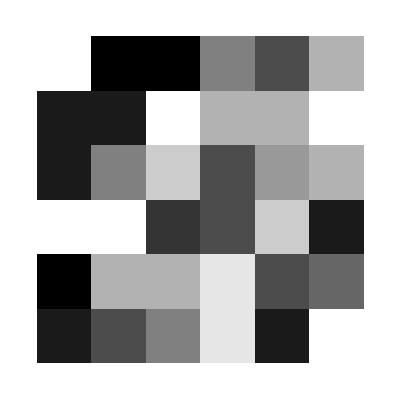

```mathematica
A//ArrayPlot
```

Notice that we obtain a 6×6 grid where the darker squares correspond to the entries int he matrix of larger value. If you prefer your plots to be more colorful, check out the options regarding ColorFunction or ColorRules.

#### Exercise 12

Create a random 20 × 20 matrix P whose entries are either 0 or 1 (each with probability 1/2). Use Table or GraphicsGrid to generate the array plots for P^i for 0 ≤ i ≤ 6. What do you notice about the plots? What might this be happening?

#### Exercise 13

Let C = {c_1, …, c_n} denote the set of all permutations of the set {1, 1, 1, 2, 2, 2, 3, 3, 3} in lexicographic/alphabetical order. Given two permutations a = a_1… a_9, b = b_1 … b_9 ∈ C, we say that a, b are transversal if (a_i, b_i)=(a_j, b_j) as ordered pairs only when i = j.

1. Generate all permutations in C in lexicographic order and assign C to be the variable containing this list. What is the cardinality of C? (That is, what is m?)

2. Write a function Transversal[a_List, b_List] which returns True if a and b are transversal and False otherwise.

3. Using Array and your function from part 2, create a matrix A whose (i,j) entry is 1 if c_i and c_j are transversal and 0 otherwise for 1 ≤ i, j ≤ m. Note that by definition the matrix will be symmetric. Verify that using SymmetricQ.

4. Generate the array plots of A^i for i ≤ 1 ≤ 4. Try messing with colors to make it look even better.